WKB for Fluctuation Operator Directly

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
sigmaTicks={0,{Pi/4,MaTeX["\\frac{\\pi}{4}",Magnification->1.2]},{Pi/2,MaTeX["\\frac{\\pi}{2}",Magnification->1.2]},{3Pi/4,MaTeX["\\frac{3\\pi}{4}",Magnification->1.2]},{Pi,MaTeX["\\pi",Magnification->1.2]}};
VV = beta*H^2 *vev^2(1/(beta* epsilon^2)- phi^2/2-b/3*(phi)^3+1/4*(phi)^4);
vPrime =D[VV,phi];
rules = {beta->45, b->25/100, epsilon->46/1000,H->1};
tol = 10^(-15);
chiMin=1/10000;
chiMax = Pi-chiMin;
phiMinR =phi/.Solve[vPrime==0,phi][[-1]];
phiMinL =phi/.Solve[vPrime==0,phi][[2]];
```

```mathematica
numpoints=200;
MyHeaviside[x_]=Piecewise[{{0,x<0},{1/2,x==0},{1,x>0}}];
chiMin=0+1/100000;
chiMax=Pi-chiMin;
```

```mathematica
ClearAll[bounceLoad]
bounceLoad[chi_]=Get["bounceJuan20DigitsExtended.wdx"];
phiFV=phi/.Solve[vPrime==0,phi][[2]]
```

1/2 (b-√(4+b^2))

```mathematica
m2Effgeneric[phi_]=D[VV,{phi,2}]/vev^2/H^2
m2ϕEff[bounce_,chi_]:=FullSimplify[(D[VV,{phi,2}]/vev^2)/H^2/.Join[rules,{phi->bounce}]];
m2ϕEffInterp = Interpolation[Table[{chi,m2ϕEff[bounceLoad[chi],chi]},{chi,chiMin,Pi,(Pi-chiMin)/200}],Method->"Spline",InterpolationOrder->2];
repPotentialRule = {VppBounce->Function[x,m2Effgeneric[phi]],VppFalse->Function[x,m2Effgeneric[phiFV]]};
repPotentialRuleNum = {VppBounce->Function[x,m2ϕEffInterp[chi]],VppFalse->Function[x,m2Effgeneric[phiFV]],H->1};
```

beta (-1-2 b phi+3 phi^2)

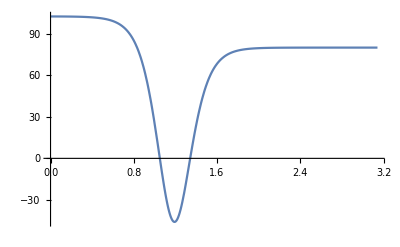
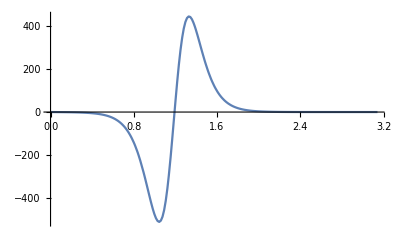
--Graphics- | -Graphics-

```mathematica
Grid[{{-Plot[m2ϕEffInterp[chi],{chi,chiMin,chiMax},PlotRange->{Automatic,Full}],
Plot[D[m2ϕEffInterp[x],x]/.{x->chi},{chi,chiMin,chiMax},PlotRange->{Automatic,Full}]}}]
```

```mathematica
(* Added the Sin factor to the deformation 15.02.2022 *)
```

```mathematica
FlucOp[f_,ell_,chi_,s_]:=(((* -3Cot[chi] D[f,chi]*)-D[D[f,chi],chi])+H^2Sin[H chi]^(-2)ell(ell+2)f+ Vpp[chi] f+s H^3/Sin[H chi]^3 f)/H^3;
```

```mathematica
ClearAll[FlucOpNoThin];
flucOpNoThin[f_,ell_,chi_,s_]:=(( -3H Cot[H chi] D[f,chi]-D[D[f,chi],chi])+H^2Sin[H chi]^(-2)ell(ell+2)f+ Vpp[chi] f+s H^3/Sin[H chi]^3f)/H^3/.Vpp->VppBounce;
```

```mathematica
solLess[ell_]:=NDSolve[{flucOpNoThin[f[chi],ell,chi,0]==0/.repPotentialRuleNum,f[chiMin]==1,f'[chiMin]==1},f,{chi,chiMin,chiMax}];
solGreat[ell_]:=NDSolve[{flucOpNoThin[f[chi],ell,chi,0]==0/.repPotentialRuleNum,f[chiMax]==1,f'[chiMax]==-1},f,{chi,chiMin,chiMax}];
```

```mathematica
fLessNum[chi_]:=f[chi]/.solLess[2][[1]]
fGreatNum[chi_]:=f[chi]/.solGreat[2][[1]]
```

```mathematica
greenHomNum [chi_]:=1/2*fLessNum[chi]*fGreatNum[chi]/Wronskian[{fGreatNum[chiP],fLessNum[chiP]},chiP]/.{chiP->chi,H->1};
```

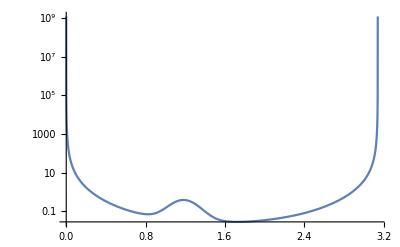

```mathematica
LogPlot[Evaluate[greenHomNum[chi]/Sin[chi]^3],{chi,chiMin,chiMax},PlotRange->{Automatic,Full}]
```

```mathematica
fless[chi_] =1/Sqrt[W[chi]] Exp[Integrate[W[chiP],{chiP,0,chi},Assumptions->{chi>0}]];
fgreat[chi_] = 1/Sqrt[W[chi]] Exp[-Integrate[W[chiP],{chiP,0,chi},Assumptions->{chi>0}]];
```

```mathematica
wkbExprLess=FullSimplify[FlucOp[fless[chi],ell,chi,s]/fless[chi],Assumptions->{0<chi<Pi}]
wkbExprGreat=FullSimplify[FlucOp[fgreat[chi],ell,chi,s]/fgreat[chi],Assumptions->{0<chi<Pi}]
```

(-3 W'[chi]^2+2 W[chi] (2 (H^2 Csc[chi H]^2 (ell (2+ell)+H s Csc[chi H])+Vpp[chi]) W[chi]-2 W[chi]^3+W''[chi]))/(4 H^3 W[chi]^2)

(-3 W'[chi]^2+2 W[chi] (2 (H^2 Csc[chi H]^2 (ell (2+ell)+H s Csc[chi H])+Vpp[chi]) W[chi]-2 W[chi]^3+W''[chi]))/(4 H^3 W[chi]^2)

```mathematica
(* W = W0 + epsilon W1 + ... *)
```

```mathematica
auxQuadraticLess =wkbExprLess-(-(3 W'[chi]^2)/(4 W[chi]^2)+((*3 Cot[chi] W'[chi]*)+W''[chi])/(2 W[chi]))/H^3==0;
auxQuadraticGreat=wkbExprGreat-(-(3 W'[chi]^2)/(4 W[chi]^2)+((*3 Cot[chi] W'[chi]*)+W''[chi])/(2 W[chi]))/H^3==0;
```

```mathematica
Worder0less[chi_]=W[chi]/.Solve[auxQuadraticLess,W[chi]][[2]]
Worder0great[chi_]=W[chi]/.Solve[auxQuadraticGreat,W[chi]][[2]]
```

√(2 ell H^2 Csc[chi H]^2+ell^2 H^2 Csc[chi H]^2+H^3 s Csc[chi H]^3+Vpp[chi])

√(2 ell H^2 Csc[chi H]^2+ell^2 H^2 Csc[chi H]^2+H^3 s Csc[chi H]^3+Vpp[chi])

```mathematica
WexpansionLess=Function[chi,Worder0less[chi]+epsilon*Worder1[chi]];
WexpansionGreat=Function[chi,Worder0great[chi]+epsilon*Worder1[chi]];
```

```mathematica
eqLess =Normal[Series[Expand[Simplify[wkbExprLess/.{W->WexpansionLess},Assumptions->{epsilon>0,0<chi<Pi}]],{epsilon,0,2}]];
eqGreat =Normal[Series[Expand[Simplify[wkbExprGreat/.{W->WexpansionGreat},Assumptions->{epsilon>0,0<chi<Pi}]],{epsilon,0,2}]];
```

$Aborted

$Aborted

```mathematica
eqWless =Simplify[Coefficient[eqLess,epsilon],Assumptions->{ell∈PositiveIntegers, 0<chi<Pi, Vpp[chi]>0}]
eqWgreat =Simplify[Coefficient[eqGreat,epsilon],Assumptions->{ell∈PositiveIntegers, 0<chi<Pi, Vpp[chi]>0}]
```

1/(4 (ell (2+ell) Csc[chi]^2+Vpp[chi])^(5/2))(-Worder1[chi] (24 ell (2+ell) Csc[chi]^2 Vpp[chi]^2+8 Vpp[chi]^3+8 ell (2+ell) Cot[chi] Csc[chi]^2 Vpp'[chi]-2 Vpp'[chi]^2+Vpp[chi] (2 ell (2+ell) (2+24 ell+12 ell^2+Cos[2 chi]) Csc[chi]^4+Vpp''[chi])+1/8 ell (2+ell) Csc[chi]^6 (16 ell (2+ell) (4 ell (2+ell)-Cos[2 chi])+8 Sin[chi]^4 Vpp''[chi]))+(ell (2+ell) Csc[chi]^2+Vpp[chi]) (3 (2 ell (2+ell) Cot[chi] Csc[chi]^2-Vpp'[chi]) Worder1'[chi]+2 (ell (2+ell) Csc[chi]^2+Vpp[chi]) Worder1''[chi]))

1/(4 (ell (2+ell) Csc[chi]^2+Vpp[chi])^(5/2))(-Worder1[chi] (24 ell (2+ell) Csc[chi]^2 Vpp[chi]^2+8 Vpp[chi]^3+8 ell (2+ell) Cot[chi] Csc[chi]^2 Vpp'[chi]-2 Vpp'[chi]^2+Vpp[chi] (2 ell (2+ell) (2+24 ell+12 ell^2+Cos[2 chi]) Csc[chi]^4+Vpp''[chi])+1/8 ell (2+ell) Csc[chi]^6 (16 ell (2+ell) (4 ell (2+ell)-Cos[2 chi])+8 Sin[chi]^4 Vpp''[chi]))+(ell (2+ell) Csc[chi]^2+Vpp[chi]) (3 (2 ell (2+ell) Cot[chi] Csc[chi]^2-Vpp'[chi]) Worder1'[chi]+2 (ell (2+ell) Csc[chi]^2+Vpp[chi]) Worder1''[chi]))

```mathematica
eqWless/.{ell->0}
```

(-Worder1[chi] (8 Vpp[chi]^3-2 Vpp'[chi]^2+Vpp[chi] Vpp''[chi])+Vpp[chi] (-3 Vpp'[chi] Worder1'[chi]+2 Vpp[chi] Worder1''[chi]))/(4 Vpp[chi]^(5/2))

```mathematica
eqW =NDSolve[ Simplify[FlucOp[fless[chi],ell,chi,0]/fless[chi]]==0,W[chi]]
```

NDSolve::argm: NDSolve called with 2 arguments; 3 or more arguments are expected.

NDSolve[ell (2+ell) Csc[chi]^2+Vpp[chi]-W[chi]^2-(3 W'[chi]^2)/(4 W[chi]^2)+W''[chi]/(2 W[chi])==0,W[chi]]

```mathematica
eqW/.{W->Function[chi,V[chi]+ell(ell+2)Csc[chi]^2]}
```

NDSolve::argm: NDSolve called with 2 arguments; 3 or more arguments are expected.

NDSolve[ell (2+ell) Csc[chi]^2-(ell (2+ell) Csc[chi]^2+V[chi])^2+Vpp[chi]-(3 (-2 ell (2+ell) Cot[chi] Csc[chi]^2+V'[chi])^2)/(4 (ell (2+ell) Csc[chi]^2+V[chi])^2)+(ell (2+ell) (4 Cot[chi]^2 Csc[chi]^2+2 Csc[chi]^4)+V''[chi])/(2 (ell (2+ell) Csc[chi]^2+V[chi]))==0,ell (2+ell) Csc[chi]^2+V[chi]]

```mathematica
fLess0[chi_] = Normal[FullSimplify[fless[chi]/.{W->Worder0less},Assumptions->{tol<chiP<Pi-tol,ell>0}]]
fGreat0[chi_] =Normal[FullSimplify[fgreat[chi]/.{W->Worder0less},Assumptions->{tol<chiP<Pi-tol,ell>0}]]
```

(ⅇ^Integrate[√(2 ell H^2 Csc[chiP H]^2+ell^2 H^2 Csc[chiP H]^2+H^3 s Csc[chiP H]^3+Vpp[chiP]),{chiP,0,chi},Assumptions→{chi>0}])/((H^2 Csc[chi H]^2 (ell (2+ell)+H s Csc[chi H])+Vpp[chi])^(1/4))

(ⅇ^(-Integrate[√(2 ell H^2 Csc[chiP H]^2+ell^2 H^2 Csc[chiP H]^2+H^3 s Csc[chiP H]^3+Vpp[chiP]),{chiP,0,chi},Assumptions→{chi>0}]))/((H^2 Csc[chi H]^2 (ell (2+ell)+H s Csc[chi H])+Vpp[chi])^(1/4))

```mathematica
Wron[chi_] =Wronskian[{fGreat0[chiP],fLess0[chiP]},chiP]/.{chiP->chi}
```

2

```mathematica
greenCoin[chi_,ell_]= (ell+1)^2Simplify[fGreat0[chi]*fLess0[chi]/Wron[chi],Assumptions->{Vpp[chi]>0,ell∈PositiveIntegers,0<chi<Pi}]
```

(1+ell)^2/(2 √(H^2 Csc[chi H]^2 (ell (2+ell)+H s Csc[chi H])+Vpp[chi]))

```mathematica
greenHom0[chi_,ell_]=(greenCoin[chi,ell]/.{Vpp->Function[x,VppBounce[x]]})-(greenCoin[chi,ell]/.{Vpp->Function[x,VppFalse[x]]})
```

(1+ell)^2/(2 √(H^2 Csc[chi H]^2 (ell (2+ell)+H s Csc[chi H])+VppBounce[chi]))-(1+ell)^2/(2 √(H^2 Csc[chi H]^2 (ell (2+ell)+H s Csc[chi H])+VppFalse[chi]))

```mathematica
correctW[chi_]=Sin[H chi]^3/H^3;
```

```mathematica
ClearAll[s]
logGreenSeries[chi_,ell_]=-1/2/correctW[chi]*Integrate[greenHom0[chi,ell],{s,0,Infinity},Assumptions->{VppBounce[chi]>0,VppFalse[chi]>0,0<chi<Pi,ell∈PositiveIntegers,Sin[chi H]>0,0<H<=1}]
```

1/2 (1+ell)^2 (√(ell (2+ell) H^2 Csc[chi H]^2+VppBounce[chi])-√(ell (2+ell) H^2 Csc[chi H]^2+VppFalse[chi]))

```mathematica
greenCoinSeries[chi_,ell_]=Collect[Expand@Simplify[Normal@Series[logGreenSeries[chi,ellPlus1-1],{ellPlus1,Infinity,3}],Assumptions->{0<chi<Pi,ellPlus1∈PositiveIntegers,Sin[chi H]>0,0<H<=1}] /.{ellPlus1->ell+1},ell+1,Simplify[#,Assumptions->{0<chi<Pi,ellPlus1∈PositiveIntegers,Csc[chi H]>0,0<H<=1}]&]
```

((1+ell) Sin[chi H] (VppBounce[chi]-VppFalse[chi]))/(4 H)-(Sin[chi H] (VppBounce[chi]-VppFalse[chi]) (-2 H^2+Sin[chi H]^2 VppBounce[chi]+Sin[chi H]^2 VppFalse[chi]))/(16 (1+ell) H^3)+(Sin[chi H] (3 H^4 VppBounce[chi]-3 H^2 Sin[chi H]^2 VppBounce[chi]^2+Sin[chi H]^4 VppBounce[chi]^3-VppFalse[chi] (3 H^4-3 H^2 Sin[chi H]^2 VppFalse[chi]+Sin[chi H]^4 VppFalse[chi]^2)))/(32 (1+ell)^3 H^5)

```mathematica
Beep[]
```

```mathematica
ClearAll[ellMax]
divergences=Expand[Simplify[Normal@Series[Sum[greenCoinSeries[chi,ell],{ell,0,Λ},Assumptions->{Λ∈PositiveIntegers,0<chi<Pi}],{Λ,Infinity,0}],Assumptions->{0<chi<Pi}]]
```

(Sin[chi H] VppBounce[chi])/(4 H)+(EulerGamma Sin[chi H] VppBounce[chi])/(8 H)+(3 Λ Sin[chi H] VppBounce[chi])/(8 H)+(Λ^2 Sin[chi H] VppBounce[chi])/(8 H)+(Log[Λ] Sin[chi H] VppBounce[chi])/(8 H)-(3 PolyGamma[2,1] Sin[chi H] VppBounce[chi])/(64 H)-(EulerGamma Sin[chi H]^3 VppBounce[chi]^2)/(16 H^3)-(Log[Λ] Sin[chi H]^3 VppBounce[chi]^2)/(16 H^3)+(3 PolyGamma[2,1] Sin[chi H]^3 VppBounce[chi]^2)/(64 H^3)-(PolyGamma[2,1] Sin[chi H]^5 VppBounce[chi]^3)/(64 H^5)-(Sin[chi H] VppFalse[chi])/(4 H)-(EulerGamma Sin[chi H] VppFalse[chi])/(8 H)-(3 Λ Sin[chi H] VppFalse[chi])/(8 H)-(Λ^2 Sin[chi H] VppFalse[chi])/(8 H)-(Log[Λ] Sin[chi H] VppFalse[chi])/(8 H)+(3 PolyGamma[2,1] Sin[chi H] VppFalse[chi])/(64 H)+(EulerGamma Sin[chi H]^3 VppFalse[chi]^2)/(16 H^3)+(Log[Λ] Sin[chi H]^3 VppFalse[chi]^2)/(16 H^3)-(3 PolyGamma[2,1] Sin[chi H]^3 VppFalse[chi]^2)/(64 H^3)+(PolyGamma[2,1] Sin[chi H]^5 VppFalse[chi]^3)/(64 H^5)

```mathematica
Collect[divergences,Sin[H chi]]
```

Sin[chi H] (VppBounce[chi]/(4 H)+(EulerGamma VppBounce[chi])/(8 H)+(3 Λ VppBounce[chi])/(8 H)+(Λ^2 VppBounce[chi])/(8 H)+(Log[Λ] VppBounce[chi])/(8 H)-(3 PolyGamma[2,1] VppBounce[chi])/(64 H)-VppFalse[chi]/(4 H)-(EulerGamma VppFalse[chi])/(8 H)-(3 Λ VppFalse[chi])/(8 H)-(Λ^2 VppFalse[chi])/(8 H)-(Log[Λ] VppFalse[chi])/(8 H)+(3 PolyGamma[2,1] VppFalse[chi])/(64 H))+Sin[chi H]^3 (-(EulerGamma VppBounce[chi]^2)/(16 H^3)-(Log[Λ] VppBounce[chi]^2)/(16 H^3)+(3 PolyGamma[2,1] VppBounce[chi]^2)/(64 H^3)+(EulerGamma VppFalse[chi]^2)/(16 H^3)+(Log[Λ] VppFalse[chi]^2)/(16 H^3)-(3 PolyGamma[2,1] VppFalse[chi]^2)/(64 H^3))+Sin[chi H]^5 (-(PolyGamma[2,1] VppBounce[chi]^3)/(64 H^5)+(PolyGamma[2,1] VppFalse[chi]^3)/(64 H^5))

```mathematica
Beep[]
```

```mathematica
ClearAll[ellMax]
D[divergences/.repPotentialRule,phi]
```

1/4 beta H^3 (-2 b+6 phi) Sin[chi]+1/8 beta EulerGamma H^3 (-2 b+6 phi) Sin[chi]+3/8 beta H^3 (-2 b+6 phi) Λ Sin[chi]+1/8 beta H^3 (-2 b+6 phi) Λ^2 Sin[chi]+1/8 beta H^3 (-2 b+6 phi) Log[Λ] Sin[chi]-3/64 beta H^3 (-2 b+6 phi) PolyGamma[2,1] Sin[chi]-1/8 beta^2 EulerGamma H^3 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Sin[chi]^3-1/8 beta^2 H^3 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Log[Λ] Sin[chi]^3+3/32 beta^2 H^3 (-2 b+6 phi) (-1-2 b phi+3 phi^2) PolyGamma[2,1] Sin[chi]^3-3/64 beta^3 H^3 (-2 b+6 phi) (-1-2 b phi+3 phi^2)^2 PolyGamma[2,1] Sin[chi]^5

```mathematica
cLog=Collect[Coefficient[divergences,Log[Λ]],Sin[chi]]
```

Sin[chi] (1/8 H^3 VppBounce[chi]-1/8 H^3 VppFalse[chi])+Sin[chi]^3 (-1/16 H^3 VppBounce[chi]^2+1/16 H^3 VppFalse[chi]^2)

```mathematica
cLinear=Coefficient[divergences,Λ]//Collect[#,Sin[chi]]&
```

Sin[chi] (3/8 H^3 VppBounce[chi]-3/8 H^3 VppFalse[chi])

```mathematica
cQuad=Coefficient[divergences,Λ^2]//Collect[#,Sin[chi]]&
```

Sin[chi] (1/8 H^3 VppBounce[chi]-1/8 H^3 VppFalse[chi])

```mathematica
cSubLin = Coefficient[divergences,Λ^(-1)]/100//.Join[repPotentialRule,rules,{phi->bounceLoad[chi]},{chi->Pi/3}]
```

0

```mathematica
cSubSubLin = Coefficient[divergences,Λ^(-2)]/100^2//.Join[repPotentialRule,rules,{phi->bounceLoad[chi]},{chi->Pi/3}]
```

0

```mathematica
cts[chi_,ellMax_]=-cLog Log[ellMax/μ]-cLinear ellMax -cQuad*ellMax^2/.repPotentialRule
```

-ellMax^2 (-1/8 (-1-b (b-√(4+b^2))+3/4 (b-√(4+b^2))^2) beta H^3+1/8 beta H^3 (-1-2 b phi+3 phi^2)) Sin[chi]-ellMax (-3/8 (-1-b (b-√(4+b^2))+3/4 (b-√(4+b^2))^2) beta H^3+3/8 beta H^3 (-1-2 b phi+3 phi^2)) Sin[chi]+Log[ellMax/μ] (-((-1/8 (-1-b (b-√(4+b^2))+3/4 (b-√(4+b^2))^2) beta H^3+1/8 beta H^3 (-1-2 b phi+3 phi^2)) Sin[chi])-(1/16 (-1-b (b-√(4+b^2))+3/4 (b-√(4+b^2))^2)^2 beta^2 H^3-1/16 beta^2 H^3 (-1-2 b phi+3 phi^2)^2) Sin[chi]^3)

#### Using the MS scheme

```mathematica
(* Model Polynomial Sin[chi]^3( delta0 + delta1 phi + 1/2 deltaM2 phi^2 + 1/3! deltab phi^3 + 1/4! deltaLambda phi^4 ) *)
delta0 =Collect[FullSimplify[D[cts[chi,Λ]/Sin[H chi]^3,{phi,0}]/.{phi->0},Assumptions->{beta>0,b>0,Λ>0,0<chi<Pi}],Csc[chi]]
delta1=Collect[ FullSimplify[D[cts[chi,Λ]/Sin[H chi]^3,{phi,1}]/.{phi->0},Assumptions->{beta>0,b>0,Λ>0,0<chi<Pi}],Csc[chi]]
deltaM2=Collect[ FullSimplify[D[cts[chi,Λ]/Sin[H chi]^3,{phi,2}]/.{phi->0},Assumptions->{beta>0,b>0,Λ>0,0<chi<Pi}],Csc[chi]]
deltab=Collect[ FullSimplify[D[cts[chi,Λ]/Sin[H chi]^3,{phi,3}]/.{phi->0},Assumptions->{beta>0,b>0,Λ>0,0<chi<Pi}],Csc[chi]]
deltaLambda=Collect[ FullSimplify[D[cts[chi,Λ]/Sin[H chi]^3,{phi,4}]/.{phi->0},Assumptions->{beta>0,b>0,Λ>0,0<chi<Pi}],Csc[chi]]
```

1/32 beta H^3 Csc[chi H]^3 Sin[chi] (-2 (-6+b (-b+√(4+b^2))) (Λ (3+Λ)+Log[Λ/μ])+(-6+b (4 √(4+b^2)-b (6+b^2-b √(4+b^2)))) beta Log[Λ/μ] Sin[chi]^2)

1/8 b beta H^3 Csc[chi H]^3 (2 Λ (3+Λ)+(2+beta-beta Cos[2 chi]) Log[Λ/μ]) Sin[chi]

1/4 beta H^3 Csc[chi H]^3 Sin[chi] (-3 (Λ (3+Λ)+Log[Λ]+Log[1/μ])+(-3+2 b^2) beta Log[Λ/μ] Sin[chi]^2)

-9/2 b beta^2 H^3 Csc[chi H]^3 Log[Λ/μ] Sin[chi]^3

27/2 beta^2 H^3 Csc[chi H]^3 Log[Λ/μ] Sin[chi]^3

```mathematica
ctsTest=FullSimplify[Sin[chi]^3( delta0 + delta1 phi + 1/2 deltaM2 phi^2 + 1/3! deltab phi^3 + 1/4! deltaLambda phi^4 ),Assumptions->{beta>0,b>0,Λ>0,0<chi<Pi}]
```

1/32 beta H^3 (-2 (-6-b^2+b √(4+b^2)-4 b phi+6 phi^2) Csc[chi]^2 (Λ (3+Λ)+Log[Λ]+Log[1/μ])+beta (-6-b^4+b^3 √(4+b^2)+6 phi^2 (-2+3 phi^2)+b^2 (-6+8 phi^2)+4 b (√(4+b^2)+2 phi-6 phi^3)) Log[Λ/μ])

```mathematica
FullSimplify[ctsTest == cts[chi,Λ],Assumptions->{beta>0,b>0,Λ>0,0<chi<Pi}]
```

True

```mathematica
ctsP[chi_,Λ_]=D[cts[chi,Λ],phi](*/.{phi->bounceLoad[chi]};*)
```

-3/8 beta H^3 (-2 b+6 phi) Λ Sin[chi]-1/8 beta H^3 (-2 b+6 phi) Λ^2 Sin[chi]+Log[Λ/μ] (-1/8 beta H^3 (-2 b+6 phi) Sin[chi]+1/8 beta^2 H^3 (-2 b+6 phi) (-1-2 b phi+3 phi^2) Sin[chi]^3)

```mathematica
FullSimplify[divergences+cts[chi,Λ]//.Join[{μ->1}],Assumptions->{b>0}]//Collect[#,Csc[chi]]&
```

1/64 H^3 Sin[chi] (8 (2+EulerGamma+3 Λ+Λ^2+Log[Λ]) VppBounce[chi]+6 VppBounce[chi] Zeta[3]+2 Sin[chi]^4 VppBounce[chi]^3 Zeta[3]-2 Sin[chi]^2 VppBounce[chi]^2 (2 (EulerGamma+Log[Λ])+3 Zeta[3])-2 (beta (phi-phiFV) (2 b-3 (phi+phiFV)) (-4 Λ (3+Λ)-(4+beta (2+2 b (phi+phiFV)-3 (phi^2+phiFV^2))) Log[Λ]+beta (2+2 b (phi+phiFV)-3 (phi^2+phiFV^2)) Cos[2 chi] Log[Λ])+VppFalse[chi] (4 (2+EulerGamma+3 Λ+Λ^2+Log[Λ])+3 Zeta[3]+Sin[chi]^2 VppFalse[chi] (-2 (EulerGamma+Log[Λ])+(-3+Sin[chi]^2 VppFalse[chi]) Zeta[3]))))

```mathematica
Zeta[3]
```

Zeta[3]

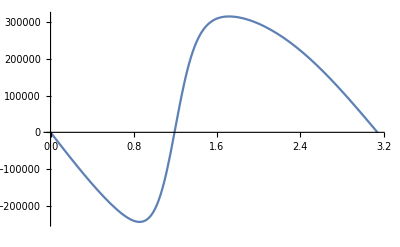

```mathematica
Plot[Evaluate[ctsP[chi,100]/.Join[rules,{phi->bounceLoad[chi],μ->1}]],{chi,chiMin,chiMax}]
```

```mathematica
Manipulate[Plot[Evaluate[Re[greenHom0[chi,ell]//.Join[repPotentialRuleNum,rules,{s->0}]]],{chi,chiMin,chiMax},PlotRange->{{tol,Pi-tol},{-0.03,0.03}}],{ell,2,100}]
```

### Estimating LogDet term with WKB/Homogeneous

```mathematica
ClearAll[finiteLogDet];
finiteLogDet[Λ_] :=Sum[NIntegrate[Re[logGreenSeries[chi,ell]]-greenCoinSeries[chi,ell]//.Join[repPotentialRuleNum,rules],{chi,chiMin,chiMax},WorkingPrecision->5],{ell,2,Λ}]
```

```mathematica
finiteLogDet[100](*Working prec. 6 *)
```

-168.65

```mathematica
finiteLogDet[300]
```

-168.97

```mathematica
finiteLogDet[800]
```

-169.

```mathematica
(* Old results before the sine correction *)
```

```mathematica
finiteLogDet[120]
```

-150.02

```mathematica
finiteLogDet[150]
```

-149.93

```mathematica
finiteLogDet[200]
```

-149.8101

```mathematica
finiteLogDet[100]
```

-150.0742

```mathematica
finiteLogDet[300]
```

-149.6807

```mathematica
finiteLogDet[800]
```

-149.489

```mathematica
ClearAll[finiteLogDetNoCot];
finiteLogDetNoCot[Λ_] :=Sum[NIntegrate[Re[logGreenSeries[chi,ell]]-greenCoinSeries[chi,ell]//.Join[repPotentialRuleNum,rules],{chi,chiMin,chiMax},WorkingPrecision->8],{ell,2,Λ}]
```

```mathematica
finiteLogDetNoCot[150]
```

-169.5759

```mathematica
finiteLogDetNoCot[200]
```

-169.64711

```mathematica
finiteLogDetNoCot[500]
```

-169.72483

```mathematica
wkbTabulated=Table[{Λ,finiteLogDetNoCot[Λ]},{Λ,10,150,20}]
```

{{10,-145.1912},{30,-166.03023},{50,-168.33223},{70,-169.00651},{90,-169.29126},{110,-169.43746},{130,-169.52232},{150,-169.5759}}

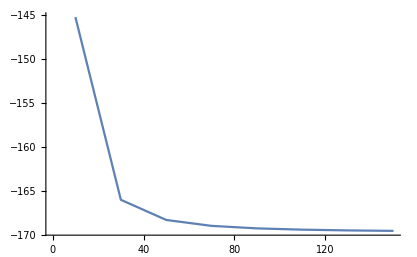

```mathematica
ListLinePlot[wkbTabulated,PlotRange->{Automatic,Full}]
```

```mathematica
Beep[]
```

```mathematica
a[chi_]=1/H*Sin[H chi]
```

Sin[chi H]/H